## Dirichlet Primes sets

```mathematica
SetDirectory[NotebookDirectory[]];
```

Sejam x e y dois primos entre si . Por exemplo, x = 5 e y = 6.
A série x, x + y, x + 2 y, x + 3 y, ... tem infinitos primos .

```mathematica
DirichletPrimes[x_,y_]=Block[{},
	Table[
		x+k y,
		{k,10000}
	]
]
```

```mathematica
coprimes=<||>;
Do[
If[CoprimeQ[x,y],coprimes[ToString@x<>" "<>ToString@y]=DirichletPrimes[x,y]],
{x,2,20},{y,2,20}
];
```

### SDL Complexity

```mathematica
Get[NotebookDirectory[]<>"sdl.mx"]
```

```mathematica
sdl[coprimes]
```

### Visibility analysis

```mathematica
Get[NotebookDirectory[]<>"visibility.mx"]
```

```mathematica
natLinks=naturalVisibilityLinks[coprimes[[2]]];
```

```mathematica
natGraph=Graph[natLinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

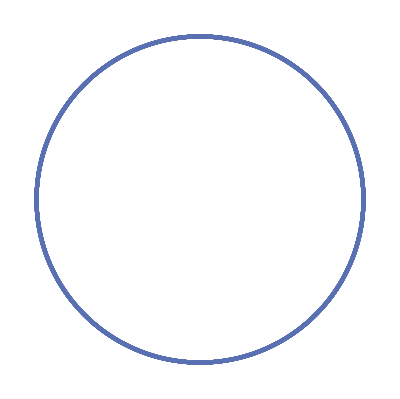

```mathematica
natGraph
```

```mathematica
Export["dirichlet.pdf",%21]
```

dirichlet.pdf

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|1→2,2→9997|>

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

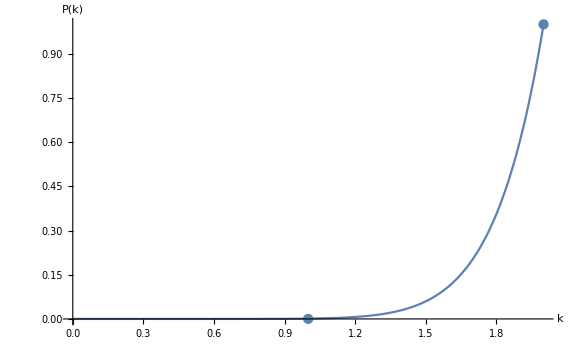
{{C→0.00112768,γ→-9.79185},-Graphics-}

```mathematica
plotModel[count,10000]
```

```mathematica
horLinks=horizontalVisibilityLinks[coprimes[[1]]];
```

```mathematica
DumpSave["horLinks.mx", horLinks];
```

```mathematica
horGraph=Graph[horLinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
count=VertexDegree[horGraph]//Counts
```

<|1→2,2→9997|>

```mathematica
horGraph
```

-Graphics-

```mathematica
Export["dirichlet-hori.pdf",%26]
```

dirichlet-hori.pdf